```mathematica
Clear[{m,a,j}]
```

```mathematica
m = 1;
a = 0.95;
j = 0.4;
```

## Event Horizons

```mathematica
(*calculates the two event horizons based on the mass and Kerr parmeter*)
rHorizonOuter = m+√(m^2-a^2);
rHorizonInner = m-√(m^2 -a^2);
```

```mathematica
(*Plotting the horizons - full spherical symmetry but limited phi to see inner sphere*)SphericalPlot3D[{rHorizonInner,rHorizonOuter},{θ,0,π},{ϕ,0,3π/2},AxesLabel->{x,y,z},PlotLegends->SwatchLegend[{Blue,Orange},{"Outer Horizon", "Inner Horizon"}],PlotLabel->Style["Event Horizon Plots", Black,FontFamily->"Times",FontSize->25,Bold]]
```

-Graphics3D-

```mathematica
Δ=r^2-2m r+a^2;
ρ2=Δ Sin[θ]^2;
Σ = (r^2+a^2)^2-Δ a^2(Sin[θ])^2;
Ω = Δ a (Cos[θ])^2;
Ξ = r^2((Cos[θ])^3-3)-a^2(1+(Cos[θ])^2);
R2 = r^2+a^2(Cos[θ])^2;
F0 = R2^2;
F1 = 4 a m Ξ( Cos[θ])R2;
F2 = 4 a^2 m^2 Ξ^2(Cos[θ])^2+Σ^2(Sin[θ])^4;
w0 = 2 a m r;
w1 = 4Cos[θ](m a^4-r^4(r-2m)-Δ a^2 r-a(r-m)Ω);
w2 =2m(3 a r^5-a^5(r+2m)+2 a^3 r^2(r+3m)-r^3((Cos[θ])^2-6)Ω+a^2 Ω((Cos[θ])^2(3r-2m)-6(r-m)));
F = (F0 +j F1+j^2 F2)/(R2 Σ (Sin[θ])^2);
W = (w0+j w1 +j^2 w2)/Σ;
```

```mathematica
Cos[θ]^2==(Cos[θ])^2
```

True

## Ergoregions

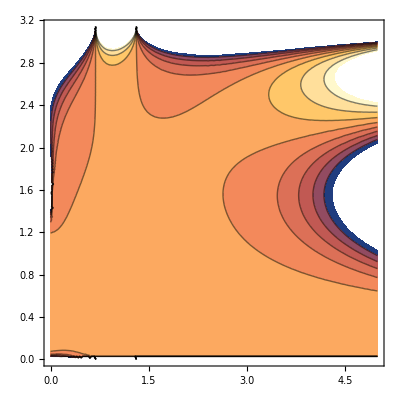

```mathematica
ContourPlot[W^2-F^2 ρ2,{r,0,5},{θ,0,π}]
```

```mathematica
Simplify[F]
```

(Csc[θ]^2 ((r^2+0.9025 Cos[θ]^2)^2+1.52 Cos[θ] (r^2+0.9025 Cos[θ]^2) (-0.9025 (1+Cos[θ]^2)+r^2 (-3+Cos[θ]^3))+0.16 (3.61 Cos[θ]^2 (-0.9025 (1+Cos[θ]^2)+r^2 (-3+Cos[θ]^3))^2+Sin[θ]^4 ((0.9025+r^2)^2-0.9025 (0.9025-2. r+r^2) Sin[θ]^2)^2)))/((r^2+0.9025 Cos[θ]^2) ((0.9025+r^2)^2-0.9025 (0.9025-2. r+r^2) Sin[θ]^2))

```mathematica
ergoregioneqn =Simplify[W^2-F^2 ρ2==0]
```

((1.9 r+0.912 r^5-0.24761 (2+r)+0.54872 r^2 (3+r)+1.30321 Cos[θ]-1.6 (-2.+r) r^4 Cos[θ]-1.444 r (0.9025-2. r+r^2) Cos[θ]-1.444 (-1.+r) (0.9025-2. r+r^2) Cos[θ]^3-0.304 r^3 (0.9025-2. r+r^2) Cos[θ]^2 (-6.+Cos[θ]^2)+0.27436 (0.9025-2 r+r^2) Cos[θ]^2 (6-6 r+(-2+3 r) Cos[θ]^2))^2-1/((r^2+0.9025 Cos[θ]^2)^2)(0.9025-2 r+r^2) Csc[θ]^2 ((r^2+0.9025 Cos[θ]^2)^2+1.52 Cos[θ] (r^2+0.9025 Cos[θ]^2) (-0.9025 (1+Cos[θ]^2)+r^2 (-3+Cos[θ]^3))+0.16 (3.61 Cos[θ]^2 (-0.9025 (1+Cos[θ]^2)+r^2 (-3+Cos[θ]^3))^2+Sin[θ]^4 ((0.9025+r^2)^2-0.9025 (0.9025-2. r+r^2) Sin[θ]^2)^2))^2)/((0.9025+r^2)^2-0.9025 (0.9025-2. r+r^2) Sin[θ]^2)^2==0

```mathematica
thetatest= Table[i,{i,0,π,0.0000001}];
rtest = Table[i,{i,0,4,0.00001}];
```

```mathematica
ergoregioneqn/.({r-> rtest,θ->π/3})
```

```mathematica
ListPlot[ergoregioneqn/.({r-> rtest,θ->π/3})]
```

ListPlot::lpn: {9.34491,9.34347,9.34204,9.34061,9.33917,9.33774,9.33631,9.33488,9.33344,9.33201,«399991»}==0 is not a list of numbers or pairs of numbers.